Caso “ibrido” di un sistema dinamico che presenta autovalori reali e compliessi e coniugati (TD)

```mathematica
A={{-1/2,0,-7/3},{-13/60,-1/5,-9/5},{1/12,0,1/3}}
```

{{-1/2,0,-7/3},{-13/60,-1/5,-9/5},{1/12,0,1/3}}

```mathematica
C1={1,0,1}
```

{1,0,1}

Calcolo gli Autovalori di A

```mathematica
λ=Eigenvalues[A]
```

{-1/5,1/12 (-1+ⅈ √3),1/12 (-1-ⅈ √3)}

```mathematica
ρ=Abs[λ[[2]]]
```

1/6

```mathematica
θ=Arg[λ[[2]]]
```

(2 π)/3

```mathematica
CharacteristicPolynomial[A,x]
```

-1/180-(11 x)/180-(11 x^2)/30-x^3

Inserisco lo stato iniziale e lo proietto lungo T

```mathematica
T0=FullSimplify[Transpose[Eigenvectors[A]]]
```

{{0,-5+ⅈ √3,-5-ⅈ √3},{1,-4+ⅈ √3,-4-ⅈ √3},{0,1,1}}

```mathematica
T0//MatrixForm
```

(0 | -5+ⅈ √3 | -5-ⅈ √3
1 | -4+ⅈ √3 | -4-ⅈ √3
0 | 1 | 1)

```mathematica
T=Transpose[{T0[[All,1]],Re[T0[[All,2]]],Im[T0[[All,2]]]}]
```

{{0,-5,√3},{1,-4,√3},{0,1,0}}

```mathematica
T//MatrixForm
```

(0 | -5 | √3
1 | -4 | √3
0 | 1 | 0)

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{-7/5},{1},{26/(5 √3)}}

Determino la forma canonica a blocchi

```mathematica
Λ=Inverse[T].A.T
```

{{-1/5,0,0},{0,-1/12,1/(4 √3)},{0,-1/(4 √3),-1/12}}

```mathematica
Λ//MatrixForm
```

(-1/5 | 0 | 0
0 | -1/12 | 1/(4 √3)
0 | -1/(4 √3) | -1/12)

Calcolo la risposta libera utilizzando la decomposizione modale

```mathematica
Subscript[x, l][k_]:=FullSimplify[T.({{λ[[1]]^k, 0, 0}, {0, ρ^k Cos[θ k], ρ^k Sin[θ k]}, {0, -ρ^k Sin[θ k], ρ^k Cos[θ k]}}).Subscript[z, 0]]
```

```mathematica
Subscript[x, l][k]
```

{{1/5 6^-k (Cos[(2 k π)/3]-(145 Sin[(2 k π)/3])/(√3))},{1/5 (-7 (-1/5)^k+6^(1-k) Cos[(2 k π)/3]-119 2^-k 3^(-1/2-k) Sin[(2 k π)/3])},{1/5 6^-k (5 Cos[(2 k π)/3]+(26 Sin[(2 k π)/3])/(√3))}}

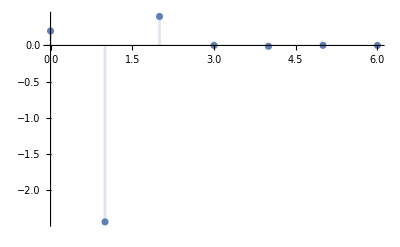

```mathematica
DiscretePlot[Subscript[x, l][k][[1]],{k,0,6},PlotRange->All]
```

```mathematica
Subscript[y, l][k_]:=FullSimplify[C1.Subscript[x, l][k]]
```

```mathematica
Subscript[y, l][k]
```

{1/5 2^-k 3^(-1-k) (18 Cos[(2 k π)/3]-119 √3 Sin[(2 k π)/3])}

```mathematica
Subscript[x, l][k]
```

{{1/5 6^-k (Cos[(2 k π)/3]-(145 Sin[(2 k π)/3])/(√3))},{1/5 (-7 (-1/5)^k+6^(1-k) Cos[(2 k π)/3]-119 2^-k 3^(-1/2-k) Sin[(2 k π)/3])},{1/5 6^-k (5 Cos[(2 k π)/3]+(26 Sin[(2 k π)/3])/(√3))}}